This code is released under the GPL license. Copyright 2018 by Valerio Marra (valerio.marra@me.com)

## 1 Preamble

```mathematica
ClearAll["Global`*"];
mvn=$VersionNumber
logD=SetDirectory[NotebookDirectory[]]
Get["code-stat/Ltools.m"];
Get["code-stat/triplotF.m"];
Get["code-stat/triplotCombo.m"];
```

11.3

/Users/rjovale/Documents/GitHub/mBayes

```mathematica
maxMemAllowed=0.8 $SystemMemory;  (* 80% of your RAM *)
Print[Row[{"Max memory allowed: ",Round[maxMemAllowed/1024^3,.1]," GB"}]];
intervalBetweenTests=1;(*seconds*)
iAmAliveSignal=0;
Dynamic[iAmAliveSignal];
RunScheduledTask[
	If[MemoryInUse[]>maxMemAllowed,Print["..quitting Mathematica, too much RAM used :S"];Quit[],iAmAliveSignal++]
,intervalBetweenTests];
```

Max memory allowed: 51.2 GB

```mathematica
(* Removes memory limit below if needed *)
(*RemoveScheduledTask[ScheduledTasks[]];*)
```

## 2 Glue code

```mathematica
(* importing your chi2 function; use "chi2=-2log L" if you need the normalization (eg for the evidence) *)
(* rname is the general label for the run; output files will start with "rname" *)
(* rname is also the name of the .m file [rename accordingly] *)

rname="JLA";
Get[ToFileName["code-phys",rname<>".m"]];
```

The reference vector is 'vectest'; the χ^2 function is 'chi2test[om,w0,wa]'

The prior vector is 'vecPtest'; the prior Fisher matrix is 'Ptest'

Dimension of parameter space: 3

```mathematica
(* setting up the chi2 function; use a vector argument *)
(* vecsolz is a reference parameter vector not far from the best-fit vector, its value is inconsequential and won't be saved *)
(* in case of a forecast, vecsolz is the fiducial value and its value is important *)

vecsolz=vectest;
chi2impz[vec_?VectorQ]:=chi2test[vec[[1]],vec[[2]],vec[[3]]];
parnamez={"Ω_m","w_0","w_a"};(* put the parameter labels (matching the dimensionality of vecsolz) *)

dpar=Length[parnamez];
Print[{parnamez,vecsolz}];
AbsoluteTiming[chi2impz[vecsolz]]
```

{{Ω_m,w_0,w_a},{0.3,-1.,0.}}

{0.008348,33.6469}

## 3 Parameter space and prior

### a Parameter space

```mathematica
run=1; (* specific label for a run *)

(* give {min,max,ngrid} for parameters p1,p2..; add more lines if necessary *)
(* it must be min < max (careful with negative quantities) *)
(* if a multivariate prior is not given (see next section), these become effectively flat priors *)
(* put all the parameters you want, you can fix them with FixSome below *)

dpar=Length[parnamez];
pSet={};

(* p1 *)
AppendTo[pSet,{.1,.5,40}];
(* p2 *)
AppendTo[pSet,{-1.4,-.6,40}];
(* p3 *)
AppendTo[pSet,{-1,1,40}];

If[Length[pSet]≠dpar,axt="Correct the parameter intervals above!";Print[axt];Speak[axt]];

redo=1; (* 0 to potentially run section 6a, 1 to never run it *)
incr=1; (* 0 to potentially run section 6b, 1 to never run it *)
adju=1; (* 0 to potentially run section 6c, 1 to never run it *)
```

```mathematica
(* here you can fix the FixPar paramters to the FixVal values  *)
FixSome=0; (* 1 to fix FixPar paramters, 0 not to *)
If[
FixSome==0
,
chi2imp[vec_]=chi2impz[vec];
vecsol=vecsolz;
parnames=parnamez;
tabpp=Range[dpar];
,
FixPar={3};
FixVal=vecsolz[[FixPar]];(* fixing the parameters to their reference value *)

tabvv=Quiet[Table[vec[[k]],{k,dpar-Length[FixPar]}]];
Do[tabvv=Insert[tabvv,FixVal[[j]],FixPar[[j]]],{j,Length[FixPar]}];
chi2imp[vec_]=chi2impz[tabvv];
tabpp=Delete[Range[dpar],Partition[FixPar,1]];
vecsol=vecsolz[[tabpp]];
parnames=parnamez[[tabpp]];
dpar=dpar-Length[FixPar];
pSet=pSet[[tabpp]];
];

tabpi=TableForm[pSet,TableHeadings->{parnames,{"min","max","grid  -  parameter intervals"}}]
```

| min | max | grid  -  parameter intervals
Ω_m | 0.1 | 0.5 | 40
w_0 | -1.4 | -0.6 | 40
w_a | -1 | 1 | 40

### b Prior

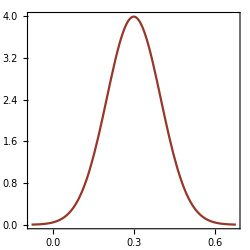
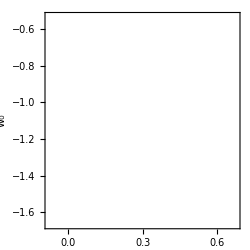
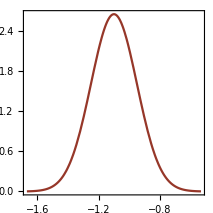
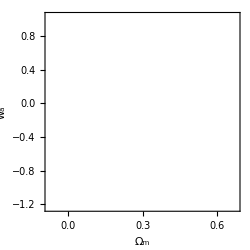
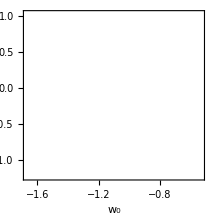
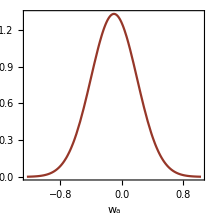
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*  0 to use flat priors from previous section, 1 to use a multivariate prior - needs Fisher and bf of the prior *)
(* as the prior bf is in general different from the likelihood bf, it does not make sense to fix parameters: dpar=Length[PMat] *)

mvprior=1;
If[
mvprior==1
,
PMat=Ptest; (* put here the Fisher matrix of your prior *)
If[Length[PMat]≠dpar,Print["Prior Fisher dimension does not match parameter space dimension"];];
CPMat=Inverse[PMat];
vecP=vecPtest; (* put here the central value of your prior *)
Prior[vec_?VectorQ]:=(2π)^(-dpar/2)Det[PMat]^(1/2) Exp[-(vec-vecP).PMat.(vec-vecP)/2];
(*chi2P[vec_?VectorQ]:=-2 Log[Prior[vec]];*)
chi2P[vec_?VectorQ]:=(vec-vecP).PMat.(vec-vecP)-Log[(2π)^(-dpar)Det[PMat]];

(* the ranges can be changed according to the prior *)
(*nriskPrior=5;(* updating ranges *)
newranges=Table[{vecP[[i]]-nriskPrior CPMat[[i,i]]^.5,vecP[[i]]+nriskPrior CPMat[[i,i]]^.5},{i,dpar}];
pSet[[All,{1,2}]]=newranges;
newtab=TableForm[pSet,TableHeadings->{parnames,{"min","max","grid  -  parameter intervals from prior"}}];
Print[newtab];*)

Print[TriPlotF[1,0,CPMat,vecP,parnames,3,{Darker[TangerineTango]}]];
,
normPrior=(Times@@Flatten[Map[Differences,pSet[[All,{1,2}]]]]);
Prior[vec_?VectorQ]:=1/normPrior; (* normalization, necessary for the evidence *)
chi2P[vec_?VectorQ]:=-2 Log[Prior[vec]]; (* step function for prior *)
];

(* the following makes the paremeter-space grid *)
ngrid=pSet[[All,3]];pMin=pSet[[All,1]];pMax=pSet[[All,2]];
(*ParSpaceTab=Table[pTabX[i,pMin,pMax,ngrid],{i,dpar}];*)
ParSpaceTab=pTabX[#,pMin,pMax,ngrid]& /@Range[dpar];
useFisher=0;
chi2[vec_]:=chi2imp[vec]+chi2P[vec];
(*chi2vec[vec_]:=Join[vec,{chi2[vec]}];*)
PLike[vec_]:=Exp[-chi2[vec]/2];
```

```mathematica
Quiet[DeleteFile[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"]]];
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{mvn,logD,parnames,PMat,CPMat,vecP,mvprior}]
```

## 4 Fisher approximation - can be skipped

{0.014169,Null}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| time in seconds | χ^2 | best-fit vector | evaluations
ConjugateGradient | 1.28286 | 25.834 | vec→{0.319743,-1.03846,-0.187557} | 7
PrincipalAxis | 0.000459 | 30.455 | vec→{0.3,-1.,0.} | 0
Newton | 1.92983 | 25.8339 | vec→{0.319894,-1.03879,-0.188492} | 7
QuasiNewton | 1.56381 | 25.8339 | vec→{0.319906,-1.03831,-0.189026} | 13

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

| time in seconds | χ^2 | best-fit vector | evaluations
ConjugateGradient | 0.489013 | 25.8339 | vec→{0.319906,-1.03831,-0.189026} | 0
PrincipalAxis | 0.886228 | 25.8339 | vec→{0.319915,-1.03844,-0.188919} | 2
Newton | 0.603057 | 25.8339 | vec→{0.319906,-1.03831,-0.189026} | 0
QuasiNewton | 0.495363 | 25.8339 | vec→{0.319906,-1.03831,-0.189026} | 0

{25.8339,{vec→{0.319915,-1.03844,-0.188919}}}
{χ_min^2,   {vec -> {Ω_m,w_0,w_a}}

Hessian calculated with 40 evaluations.

L=(1603.07 | 466.635 | 308.406
466.635 | 274. | 123.689
308.406 | 123.689 | 135.445)       L^-1=(0.0014528 | -0.00166886 | -0.00178398
-0.00166886 | 0.00812645 | -0.00362114
-0.00178398 | -0.00362114 | 0.014752)

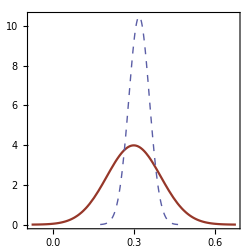
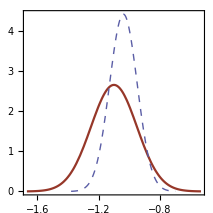
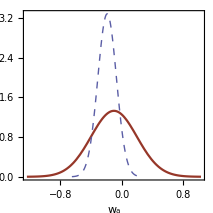
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
comboLP=1; (* 0 to do Fisher on the Likelihood, 1 to do Fisher on Prior*Likelihood - this may be necessary if the Likelihood is too degenerated *)
forecast=0; (* 1 if a forecast is considered; skips the minimization *)

NumChi2=2; (* 0 if chi2imp is analytic - the only implication is how the Hessian (Fisher matrix) is computed *)
(* 1 for NHessian package, 2 for built-in experimental Mathematica function (also suitable for non-numerical functions) *)
scaleNH=10^-2.5; (* NHessian package fudge parameter *)
orderHes=3; (* order used by the built-in experimental Mathematica function *)

If[mvprior==0,comboLP=0];
If[
comboLP==0

,

If[
forecast==0
,
(* minimum chi2 *)
fmMethods={"ConjugateGradient","PrincipalAxis","Newton","QuasiNewton"};
LaunchKernels[Length[fmMethods]];
(*Print[AbsoluteTiming[DistributeDefinitions["Global`"];]];*)
Print[AbsoluteTiming[DistributeDefinitions[fmMethods,chi2imp];]];
tabfm1=ParallelTable[
Off[General::partd,FindMinimum::fddis,FindMinimum::bdmtd];AbsoluteTiming[cout=0;{FindMinimum[chi2imp[vec],{vec,vecsol,pSet[[All,1]],pSet[[All,2]]},Method->i,StepMonitor:>cout++],cout}]
,{i,fmMethods}];
(*CloseKernels[];*)
Print[TableForm[Partition[Flatten[tabfm1,3],4],TableHeadings->{fmMethods,{"time in seconds","χ^2","best-fit vector","evaluations"}}]];
sortabfm1=Sort[tabfm1[[All,2,1]],#1[[1]]<#2[[1]]&];
beffi=sortabfm1[[1]];
chi2minfi=beffi[[1]];vecL=vec/.beffi[[2]];

tabfm1=ParallelTable[
Off[General::partd,FindMinimum::fddis,FindMinimum::bdmtd];AbsoluteTiming[cout=0;{FindMinimum[chi2imp[vec],{vec,vecL,pSet[[All,1]],pSet[[All,2]]},Method->i,StepMonitor:>cout++],cout}]
,{i,fmMethods}];
CloseKernels[];
Print[TableForm[Partition[Flatten[tabfm1,3],4],TableHeadings->{fmMethods,{"time in seconds","χ^2","best-fit vector","evaluations"}}]];
sortabfm1=Sort[tabfm1[[All,2,1]],#1[[1]]<#2[[1]]&];
beffi=sortabfm1[[1]];
chi2minfi=beffi[[1]];vecL=vec/.beffi[[2]];
,
vecL=vecsol;
chi2minfi=0; (* it is usually the case *)
beffi={chi2minfi,vecL};
];
testFin=Total@Boole[Table[vecL[[i]]==pSet[[i,1]]||vecL[[i]]==pSet[[i,2]],{i,dpar}]];
Print[Column[{"",beffi,Row[{"{χ_min^2,   {vec -> ",parnames,"}"}],""}]];

If[
testFin==0
,
Which[
NumChi2==0
,
LMat=1/2D[chi2imp[Table[x[i],{i,dpar}]],{Table[x[i],{i,dpar}],2}]/.Table[x[i]->vecL[[i]],{i,dpar}];
,
NumChi2==1
,
Get["code-stat/NHessian.m"];
Hscale=If[Total@Boole[Map[Equal[#,0]&,vecL]]==0,Abs[vecL]scaleNH,10^-3]; (* in the rare case that a bf value is zero... *)
chi2impt[vec_]:=(coc++;chi2imp[vec]);
coc=0;
LMat=1/2NHessian[chi2impt,vecL,Scale->Hscale];
Print[Row[{"NHessian calculated with ",coc," evaluations."}]];
,
NumChi2==2
,
authes=Block[{e=0},
{f=Experimental`CreateNumericalFunction[Table[Subscript[x,i],{i,dpar}],chi2imp[Table[Subscript[x,i],{i,dpar}]],{},Hessian->{Automatic,"DifferenceOrder"->orderHes},EvaluationMonitor:>e++];f["Hessian"[vecL]],e}];
LMat=1/2authes[[1]];
Print[Row[{"Hessian calculated with ",authes[[2]]," evaluations."}]];
];
Print["L=",MatrixForm[LMat],"       L^-1=",MatrixForm[CLMat=Inverse[LMat]]];Print[" "];
testE=Map[(#>0)&,Eigenvalues[CLMat]];

If[
Times@@(Boole[testE])≠1
,
Print["Fisher went wrong! C is not positive definite!"];
useFisher=0;
,
useFisher=1;
(* Fisher approximation for likelihood and corresponding chi2 *)
Lmax=Exp[-chi2minfi/2];
LikeL[vec_?VectorQ]:=Lmax Exp[-(vec-vecL).LMat.(vec-vecL)/2];
(*chi2L[vec_?VectorQ]:=-2 Log[LikeL[vec]];*)
chi2L[vec_?VectorQ]:=chi2minfi+(vec-vecL).LMat.(vec-vecL);
chi2F[vec_]:=chi2L[vec]+chi2P[vec];

Print[triplotL=TriPlotF[2,0,CLMat,vecL,parnames,3,{Darker[Emerald]}]];
];
,
Print["Min χ^2 outside prior intervals! Fisher can't be used."];
useFisher=0;
];

Which[
mvprior==1&&useFisher==1
,
(* combined Fisher and ML estimator *)
FMat=LMat+PMat;
CFMat=Inverse[FMat];
vecF=CFMat.(LMat.vecL+PMat.vecP);
chi2minfiF=chi2[vecF];

TriPlotF[3,0,CFMat,vecF,parnames,3,{Thick,Dashed,Iris}];
Print[triplotF=TriPlotCombo[{1,2,3}]];
Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot_Fisher.pdf"],triplotF,"AllowRasterization"->True,ImageResolution->400];
,
useFisher==1
,
FMat=LMat;
CFMat=CLMat;
vecF=vecL;
chi2minfiF=chi2[vecF];

Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot_Fisher.pdf"],triplotL,"AllowRasterization"->True,ImageResolution->400];
];

,

If[
forecast==0
,
(* minimum chi2 *)
fmMethods={"ConjugateGradient","PrincipalAxis","Newton","QuasiNewton"};
LaunchKernels[Length[fmMethods]];
(*Print[AbsoluteTiming[DistributeDefinitions["Global`"];]];*)
Print[AbsoluteTiming[DistributeDefinitions[fmMethods,chi2];]];
tabfm1=ParallelTable[
Off[General::partd,FindMinimum::fddis,FindMinimum::bdmtd];AbsoluteTiming[cout=0;{FindMinimum[chi2[vec],{vec,vecsol,pSet[[All,1]],pSet[[All,2]]},Method->i,StepMonitor:>cout++],cout}]
,{i,fmMethods}];
(*CloseKernels[];*)
Print[TableForm[Partition[Flatten[tabfm1,3],4],TableHeadings->{fmMethods,{"time in seconds","χ^2","best-fit vector","evaluations"}}]];
sortabfm1=Sort[tabfm1[[All,2,1]],#1[[1]]<#2[[1]]&];
beffi=sortabfm1[[1]];
chi2minfiF=beffi[[1]];vecF=vec/.beffi[[2]];

tabfm1=ParallelTable[
Off[General::partd,FindMinimum::fddis,FindMinimum::bdmtd];AbsoluteTiming[cout=0;{FindMinimum[chi2[vec],{vec,vecF,pSet[[All,1]],pSet[[All,2]]},Method->i,StepMonitor:>cout++],cout}]
,{i,fmMethods}];
CloseKernels[];
Print[TableForm[Partition[Flatten[tabfm1,3],4],TableHeadings->{fmMethods,{"time in seconds","χ^2","best-fit vector","evaluations"}}]];
sortabfm1=Sort[tabfm1[[All,2,1]],#1[[1]]<#2[[1]]&];
beffi=sortabfm1[[1]];
chi2minfiF=beffi[[1]];vecF=vec/.beffi[[2]];
,
vecF=vecsol;
chi2minfiF=0; (* it is usually the case *)
beffi={chi2minfiF,vecF};
];
testFin=Total@Boole[Table[vecF[[i]]==pSet[[i,1]]||vecF[[i]]==pSet[[i,2]],{i,dpar}]];
Print[Column[{"",beffi,Row[{"{χ_min^2,   {vec -> ",parnames,"}"}],""}]];

If[
testFin==0
,
Which[
NumChi2==0
,
FMat=1/2D[chi2[Table[x[i],{i,dpar}]],{Table[x[i],{i,dpar}],2}]/.Table[x[i]->vecF[[i]],{i,dpar}];
,
NumChi2==1
,
Get["code-stat/NHessian.m"];
Hscale=If[Total@Boole[Map[Equal[#,0]&,vecF]]==0,Abs[vecF]scaleNH,10^-3]; (* in the rare case that a bf value is zero... *)
chi2impt[vec_]:=(coc++;chi2[vec]);
coc=0;
FMat=1/2NHessian[chi2impt,vecF,Scale->Hscale];
Print[Row[{"NHessian calculated with ",coc," evaluations."}]];
,
NumChi2==2
,
authes=Block[{e=0},
{fhesx=Experimental`CreateNumericalFunction[Table[Subscript[x,i],{i,dpar}],chi2[Table[Subscript[x,i],{i,dpar}]],{},Hessian->{Automatic,"DifferenceOrder"->orderHes},EvaluationMonitor:>e++];fhesx["Hessian"[vecF]],e}];
FMat=1/2authes[[1]];
Print[Row[{"Hessian calculated with ",authes[[2]]," evaluations."}]];
];
Print["L=",MatrixForm[FMat],"       L^-1=",MatrixForm[CFMat=Inverse[FMat]]];Print[" "];
testE=Map[(#>0)&,Eigenvalues[CFMat]];

If[
Times@@(Boole[testE])≠1
,
Print["Fisher went wrong! C is not positive definite!"];
useFisher=0;
,
useFisher=1;
(* Fisher approximation for likelihood and corresponding chi2 *)
Lmax=Exp[-chi2minfiF/2];
LikeF[vec_?VectorQ]:=Lmax Exp[-(vec-vecF).FMat.(vec-vecF)/2];
(*chi2F[vec_?VectorQ]:=-2 Log[LikeF[vec]];*)
chi2F[vec_?VectorQ]:=chi2minfiF+(vec-vecF).FMat.(vec-vecF);

TriPlotF[3,0,CFMat,vecF,parnames,3,{Thick,Dashed,Iris}];
Print[triplotF=TriPlotCombo[{1,3}]];
Export[ToFileName["results-analysis",rname<>"-run"<>ToString[run]<>"-triplot_Fisher.pdf"],triplotF,"AllowRasterization"->True,ImageResolution->400];
];
,
Print["Min χ^2 outside prior intervals! Fisher can't be used."];
useFisher=0;
];

];

PosteriorF[vec_?VectorQ]:=(2π)^(-dpar/2)Det[FMat]^(1/2) Exp[-(vec-vecF).FMat.(vec-vecF)/2];
```

```mathematica
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{vecL,LMat,CLMat,chi2minfi,chi2minfiF,vecF,FMat,CFMat,useFisher,comboLP}]
```

## 5 Adjusting intervals using Fisher - can be skipped

### a Reducing grid intervals (intersection)

```mathematica
nrisk=5; (* for automatic parameter intervals of vecF ± nrisk sigma *)

If[
useFisher==1&&redo==0
,
redo=1;
gridspo=pSet[[All,{1,2}]];
extremaF={};
Do[
AppendTo[extremaF,auxex={vecF[[i]]-nrisk CFMat[[i,i]]^.5,vecF[[i]]+nrisk CFMat[[i,i]]^.5}];
popo1=Plot[PDF[NormalDistribution[vecF[[i]],CFMat[[i,i]]^.5],x],{x,auxex[[1]],auxex[[2]]},PlotRange->All,Frame->True,FrameStyle->12,FrameLabel->parnames[[i]],ImageSize->300,Axes->False,PlotStyle->Darker[Emerald],FrameTicks->{Automatic,None}];
popo2=Plot[0,{x,gridspo[[i,1]],gridspo[[i,2]]},PlotRange->{All,{0,(2 π CFMat[[i,i]])^-.5}},Filling->Top,PlotStyle->None,FillingStyle->Directive[Opacity[0.15],Emerald]];
popo[i]=Show[popo1,popo2];
,{i,dpar}];
Print[GraphicsRow[Table[popo[i],{i,dpar}],PlotLabel->Row[{Style["Suggested nrisk-intervals (x-axes) and original intervals ",16],Style["(green areas)",16,Background->Directive[Opacity[0.15],Emerald]]}],Spacings->Scaled[-.2]]];

(* this updates the intervals *)
pSet[[All,{1,2}]]=Map[{Min[#],Max[#]}&,Map[IntervalIntersection[Interval[#[[1]]],Interval[#[[2]]]]&,Transpose[{extremaF,pSet[[All,{1,2}]]}]]];
];

(* the following makes the paremeter-space grid *)
ngrid=pSet[[All,3]];pMin=pSet[[All,1]];pMax=pSet[[All,2]];
(*ParSpaceTab=Table[pTabX[i,pMin,pMax,ngrid],{i,dpar}];*)
ParSpaceTab=pTabX[#,pMin,pMax,ngrid]& /@Range[dpar];

TableForm[pSet,TableHeadings->{parnames,{"min","max","grid  -  updated parameter intervals"}}]
```

| min | max | grid  -  updated parameter intervals
Ω_m | 0.1 | 0.5 | 40
w_0 | -1.4 | -0.6 | 40
w_a | -1 | 1 | 40

### b Increasing grid intervals (union)

```mathematica
nrisk=5; (* for automatic parameter intervals of vecF ± nrisk sigma *)

If[
useFisher==1&&incr==0
,
incr=1;
gridspo=pSet[[All,{1,2}]];
extremaF={};
Do[
AppendTo[extremaF,auxex={vecF[[i]]-nrisk CFMat[[i,i]]^.5,vecF[[i]]+nrisk CFMat[[i,i]]^.5}];
popo1=Plot[PDF[NormalDistribution[vecF[[i]],CFMat[[i,i]]^.5],x],{x,auxex[[1]],auxex[[2]]},PlotRange->All,Frame->True,FrameStyle->12,FrameLabel->parnames[[i]],ImageSize->300,Axes->False,PlotStyle->Darker[Emerald],FrameTicks->{Automatic,None}];
popo2=Plot[0,{x,gridspo[[i,1]],gridspo[[i,2]]},PlotRange->{All,{0,(2 π CFMat[[i,i]])^-.5}},Filling->Top,PlotStyle->None,FillingStyle->Directive[Opacity[0.15],Emerald]];
popo[i]=Show[popo1,popo2];
,{i,dpar}];
Print[GraphicsRow[Table[popo[i],{i,dpar}],PlotLabel->Row[{Style["Suggested nrisk-intervals (x-axes) and original intervals ",16],Style["(green areas)",16,Background->Directive[Opacity[0.15],Emerald]]}],Spacings->Scaled[-.2]]];

(* this updates the intervals *)
pSet[[All,{1,2}]]=Map[{Min[#],Max[#]}&,Map[IntervalUnion[Interval[#[[1]]],Interval[#[[2]]]]&,Transpose[{extremaF,pSet[[All,{1,2}]]}]]];
];

(* the following makes the paremeter-space grid *)
ngrid=pSet[[All,3]];pMin=pSet[[All,1]];pMax=pSet[[All,2]];
(*ParSpaceTab=Table[pTabX[i,pMin,pMax,ngrid],{i,dpar}];*)
ParSpaceTab=pTabX[#,pMin,pMax,ngrid]& /@Range[dpar];

TableForm[pSet,TableHeadings->{parnames,{"min","max","grid  -  updated parameter intervals"}}]
```

| min | max | grid  -  updated parameter intervals
Ω_m | 0.1 | 0.5 | 40
w_0 | -1.4 | -0.6 | 40
w_a | -1 | 1 | 40

### c Adjusting grid intervals (Fisher only)

```mathematica
nrisk=5; (* for automatic parameter intervals of vecF ± nrisk sigma *)

If[
useFisher==1&&adju==0
,
adju=1;
gridspo=pSet[[All,{1,2}]];
extremaF={};
Do[
AppendTo[extremaF,auxex={vecF[[i]]-nrisk CFMat[[i,i]]^.5,vecF[[i]]+nrisk CFMat[[i,i]]^.5}];
popo1=Plot[PDF[NormalDistribution[vecF[[i]],CFMat[[i,i]]^.5],x],{x,auxex[[1]],auxex[[2]]},PlotRange->All,Frame->True,FrameStyle->12,FrameLabel->parnames[[i]],ImageSize->300,Axes->False,PlotStyle->Darker[Emerald],FrameTicks->{Automatic,None}];
popo2=Plot[0,{x,gridspo[[i,1]],gridspo[[i,2]]},PlotRange->{All,{0,(2 π CFMat[[i,i]])^-.5}},Filling->Top,PlotStyle->None,FillingStyle->Directive[Opacity[0.15],Emerald]];
popo[i]=Show[popo1,popo2];
,{i,dpar}];
Print[GraphicsRow[Table[popo[i],{i,dpar}],PlotLabel->Row[{Style["Suggested nrisk-intervals (x-axes) and original intervals ",16],Style["(green areas)",16,Background->Directive[Opacity[0.15],Emerald]]}],Spacings->Scaled[-.2]]];

(* this updates the intervals *)
pSet[[All,{1,2}]]=extremaF;
];

(* the following makes the paremeter-space grid *)
ngrid=pSet[[All,3]];pMin=pSet[[All,1]];pMax=pSet[[All,2]];
(*ParSpaceTab=Table[pTabX[i,pMin,pMax,ngrid],{i,dpar}];*)
ParSpaceTab=pTabX[#,pMin,pMax,ngrid]& /@Range[dpar];

TableForm[pSet,TableHeadings->{parnames,{"min","max","grid  -  updated parameter intervals"}}]
```

| min | max | grid  -  updated parameter intervals
Ω_m | 0.1 | 0.5 | 40
w_0 | -1.4 | -0.6 | 40
w_a | -1 | 1 | 40

### d Flat prior (re)normalization

```mathematica
If[
mvprior==0
,
normPrior=(Times@@Flatten[Map[Differences,pSet[[All,{1,2}]]]]);
Prior[vec_?VectorQ]:=1/normPrior; (* normalization, necessary for the evidence *)
chi2P[vec_?VectorQ]:=-2 Log[Prior[vec]]; (* step function for prior *)
chi2minfiF=chi2[vecF];
];
```

```mathematica
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{chi2minfiF}]
```

## 6 n-Evidence - can be skipped

```mathematica
nEvi=5;
Which[
mvprior==1&&useFisher==1&&comboLP==1
,
FEvi=Lmax (2π)^(dpar/2)Det[FMat]^(-1/2);
NEvi=NEvidence[vecF,FMat,nEvi];
NFEvi=PLike[vecF]/PosteriorF[vecF];
,
mvprior==1&&useFisher==1
,
(* see eq.(14) of arXiv:1209.1897 *)
FEvi=Lmax (Det[PMat]/ Det[FMat])^(1/2) Exp[-1/2 (vecL-vecP).(LMat.Inverse[FMat].PMat).(vecL-vecP)];
NEvi=NEvidence[vecF,FMat,nEvi];
NFEvi=PLike[vecF]/PosteriorF[vecF];
,
useFisher==1
,
FEvi=1/normPrior Lmax (2π)^(dpar/2)Det[LMat]^(-1/2);
NEvi= NEvidence[vecL,LMat,nEvi];
NFEvi=PLike[vecL]/PosteriorF[vecL];
];

Print[Row[{"Fisher evidence: Log E=",logFEvi=Chop[Log[FEvi]]}]];
Print[Row[{"Numeric evidence: Log E=",logNEvi=Log[NEvi],"  -  limiting the integration within the n-σ Fisher ellipsoid"}]];
Print[Row[{"'Numeric' Fisher: Log E=",logFNEvi=Log[NFEvi]}]];
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{logNEvi,logFEvi}];
```

Fisher evidence: Log E=-18.4224

Numeric evidence: Log E=-18.4678  -  limiting the integration within the n-σ Fisher ellipsoid

'Numeric' Fisher: Log E=-18.4224

```mathematica
(* (normalized) posterior distribution *)
Posterior[vec_?VectorQ]:=PLike[vec]/NEvi;
PosteriorF2[vec_?VectorQ]:=PLike[vec]/FEvi;

{Posterior[vecF],PosteriorF2[vecF],PosteriorF[vecF]}
{Posterior[vecsol],PosteriorF2[vecsol],PosteriorF[vecsol]}
```

{257.464,246.028,246.028}

{25.5416,24.4071,24.2261}

## 7 chi2 table

### a Preparation

```mathematica
LaunchKernels[]
ncompkern=Length[Kernels[]]
```

{KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local]}

10

```mathematica
nco=32; (* number of points to be computed in order to estimate total time - not working well *)
ere=1;
ParallelTable[ere=RandomReal[{.9,1.1}];AbsoluteTiming[chi2[Evaluate[vecsol ere]];][[1]],{$KernelCount}]; (* to load stuff *)
AbsoluteTiming[auxte=ParallelTable[ere=RandomReal[{.9,1.1}];AbsoluteTiming[chi2[Evaluate[vecsol ere]];][[1]],{nco}];];
tempo1=Total[auxte]/$KernelCount/nco;

glevel=0; (* restricting the grid to within the glevel-σ Fisher ellipsoid; 0 for a full exploration *)
If[
useFisher==1&&glevel≠0
,
(*alevel=(x/.FindRoot[CDF[ChiSquareDistribution[dpar],x]==v[glevel],{x,10}])^.5;*)
alevel=levhi2[dpar,glevel]^(1/2);
(*chi2vecx[vec_]:=If[gtest[vec,alevel,FMat,vecF],chi2vec[vec],Join[vec,{chi2F[vec]}]];*)
chi2x[vec_]:=If[gtest[vec,alevel,FMat,vecF],chi2[vec],chi2F[vec]];(* using Fisher to give the right order of magnitude *)
(*Print[AbsoluteTiming[ppTab=ParallelTable[(btest[take[ParSpaceTab,{i,i}][[1]],alevel,FMat,vecF]),{i,Times@@ngrid}];]];
Print[tpoints=Total[ppTab]];*)
(* volume glevel-σ Fisher ellipsoid over total volume *)
volratio=(π^(dpar/2)/Gamma[dpar/2+1] glevel^dpar Times@@Sqrt[Eigenvalues[CFMat]])/(Times@@Flatten[Differences/@pSet[[All,{1,2}]]]);
Print[Row[{"Volume reduction: ",Round[1/volratio,.1]}]];
tpoints=volratio Times@@ngrid;
Print[estime1=Row[{"Estimated wall-clock time: ",tpoints tempo1/60," min or ",tpoints tempo1/60^2," hours"}]];
Print[Row[{"Posterior exploration will end on ",DatePlus[Quantity[tpoints tempo1,"Seconds"]]}]];
Print[estime2=Row[{"Total number of points: ",Round[tpoints]," instead of ",Times@@ngrid}]];
,
(*chi2vecx[vec_]:=chi2vec[vec];*)
chi2x[vec_]:=chi2[vec];
Print[estime1=Row[{"Estimated wall-clock time: ",Times@@ngrid tempo1/60," min or ",Times@@ngrid tempo1/60^2," hours"}]];
Print[Row[{"Posterior exploration will end on ",DatePlus[Quantity[Times@@ngrid tempo1,"Seconds"]]}]];
Print[estime2=Row[{"Total number of points: ",Times@@ngrid}]];
];
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{ncompkern,estime1,estime2}]
```

Estimated wall-clock time: 0.69471 min or 0.0115785 hours

Attributes::notfound: Symbol SymbolicTensors`Metrize not found.

Posterior exploration will end on Fri 18 May 2018 17:45:12GMT-3.

Total number of points: 64000

### b Computation

```mathematica
AbsoluteTiming[DistributeDefinitions["Global`"];]

tta = SessionTime[];
(*chi2Tab=ParallelMap[(chi2[#])&,Tuples[ParSpaceTab]];*)
chi2Tab=ParallelTable[chi2x[take[ParSpaceTab,{i,i}][[1]]],{i,Times@@ngrid}];
dtt=SessionTime[]-tta;
(*pronto*)

Row[{"Calculation ended on ",DateString[]}]
Row[{Round[dtt/60^2,.1],"h or ",Round[dtt/60,.1],"m of total computation"}]
Row[{Round[dtt/(Times@@ngrid),.001],"s per grid point"}]
logrun=Row[{"Calculation ended on ",DateString[],"  -  ",Round[dtt/60^2,.1],"h or ",Round[dtt/60,.1],"m of total computation  -  ",Round[dtt/(Times@@ngrid),.00001],"s per grid point"}];
```

{1.15007,Null}

Calculation ended on Fri 18 May 2018 17:45:25

0.h or 0.9m of total computation

0.001s per grid point

```mathematica
(* sanity check *)
stest=Total[Im[chi2Tab[[All]]]];If[stest≠ 0,"something funny is going on..."]
```

```mathematica
Save[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>"-log.txt"],{pSet,logrun}]
Export[ToFileName["results-chi2",rname<>"_run"<>ToString[run]<>".r32"],Flatten[Re[chi2Tab]],"Real32"]
```

results-chi2/JLA_run1.r32

### c End

```mathematica
CloseKernels[];
NotebookSave[];
Quit[];
```